```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
playerX = 3.456;
playerY = 2.345;
playerAngle =  1.523;

map=Map[Characters,{
"0000222222220000", 
"1              0",
"1      11111   0",
"1     0        0",
"0     0  1110000",
"0     3        0",
"0   10000      0",
"0   0   11100  0",
"0   0   0      0",
"0   0   1  00000",
"0       1      0",
"2       1      0",
"0       0      0",
"0 0000000      0",
"0              0", 
"0002222222200000"
}];
replaceRules = {" "->0,"0"->1,"1"->2,"2"->3};
```

```mathematica
RayProject[{posX_,posY_},angle_,distance_]:={posX+distance*Cos[angle],posY+distance*Sin[angle]};
RayCast[{posX_,posY_},angle_,delta_ : 0.2]:=Block[{intersection,d = 0.1},
intersection = " ";
While[intersection == " ",
intersection = Extract[map,Floor[RayProject[{posX,posY},angle,d]]];
d+=delta;
];
Return[d-delta];
];
```

```mathematica
RayCast[{playerX,playerY},playerAngle]
```

5.7

```mathematica
Floor@RayProject[{playerX,playerY},playerAngle,5.700000000000003]
```

{3,8}

```mathematica
Extract[map,{3,8}]
```

1

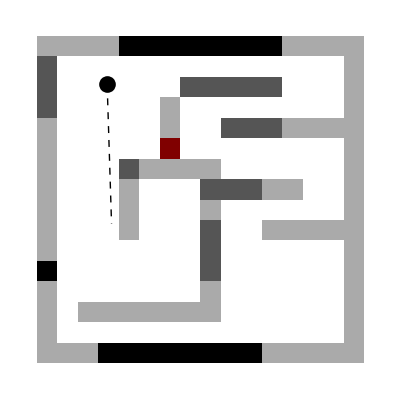

```mathematica
Show[
ArrayPlot[map/.replaceRules],
Graphics[
{
{PointSize[0.03],Point[{playerX,16-playerY}]},
{Dashed,Line[{{playerX,16-playerY},RayProject[{playerX,playerY},playerAngle,RayCast[{playerX,playerY},playerAngle]]}]}
}
]
]
```